

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
FullSimplify[Normalize@{t^2,t(t t-1)},t∈Reals]
```

{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))}

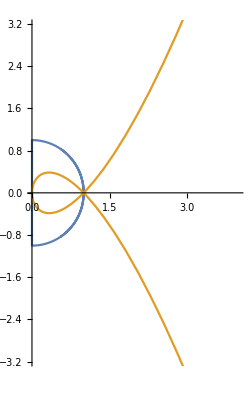

```mathematica
ParametricPlot[{
{Abs[t]/(√(1-t^2+t^4)),(t (-1+t^2))/(√(t^2-t^4+t^6))},
{t^2,t(t t-1)}
},{t,-2,2}]
```

```mathematica
2{Cos[t],Sin[t]}
```

{2 Cos[t],2 Sin[t]}

```mathematica
FullSimplify[Normalize@{2 Cos[t],2 Sin[t]},t∈Reals]
```

{Cos[t],Sin[t]}

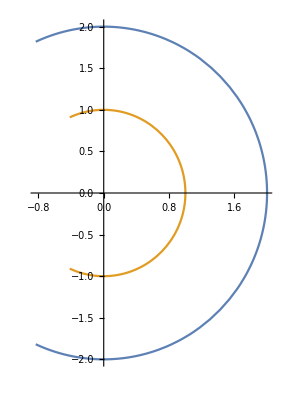

```mathematica
ParametricPlot[{
{2Cos[t],2Sin[t]},
{Cos[t],Sin[t]}
},{t,-2,2}]
```

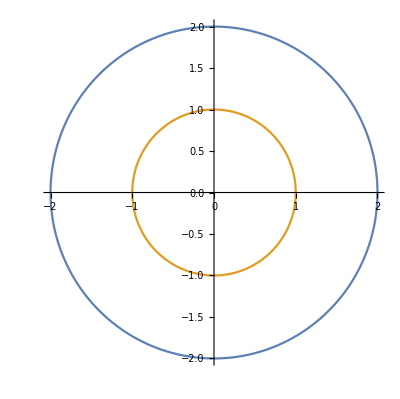

```mathematica
ParametricPlot[{
{2Cos[t],2Sin[t]},
{Cos[t],Sin[t]}
},{t,0,2π}]
```

```mathematica
{t,Sin[t]}.RotationMatrix[2π-π/4]
```

{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}

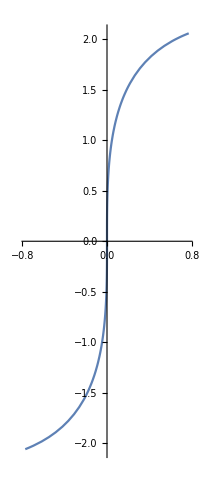

```mathematica
ParametricPlot[
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)}
,{t,-2,2}]
```

```mathematica
FullSimplify[Normalize@{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},t∈Reals]
```

{(t-Sin[t])/(√2 √(t^2+Sin[t]^2)),(t+Sin[t])/(√(1+2 t^2-Cos[2 t]))}

```mathematica
Manipulate[
ParametricPlot[{
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},
{(t-Sin[t])/(√2 √(t^2+Sin[t]^2)),(t+Sin[t])/(√(1+2 t^2-Cos[2 t]))}
},{t,-2,-2+a}]
,{a,0.01,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},
{(t-Sin[t])/(√2 √(t^2+Sin[t]^2)),(t+Sin[t])/(√(1+2 t^2-Cos[2 t]))}
},{t,-2,-2+a},PlotRange->{{-3,3},{-3,3}}]
,{a,0.01,4}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},
{(t-Sin[t])/(√2 √(t^2+Sin[t]^2)),(t+Sin[t])/(√(1+2 t^2-Cos[2 t]))}
},{t,-2,-2+a},PlotRange->{{-3,3},{-3,3}}]
,{a,0.01,8}]
```

```mathematica
Manipulate[
ParametricPlot[{
{t/(√2)-Sin[t]/(√2),t/(√2)+Sin[t]/(√2)},
{(t-Sin[t])/(√2 √(t^2+Sin[t]^2)),(t+Sin[t])/(√(1+2 t^2-Cos[2 t]))}
},{t,-8,-8+a},PlotRange->{{-3,3},{-3,3}}]
,{a,0.01,16}]
```